Application I: ϕ^4-theory

This notebook demonstrates how to use the following packages:
	Basis-Scalar.wl
	MatrixElements-Scalar.wl
to generate the basis and matrix elements for ϕ^4 theory. We also show how to use the output data to reproduce Figures 12-17 in the paper.

# Set DMAX and Directory (RUN FIRST)

EVALUATE THIS CELL FIRST
This notebook is designed such that you construct and save the basis and matrix elements once, for some large value DMAX, then always use those reference files to extract data for any Δmax ≤ DMAX. This cell sets the value of DMAX, which will be used in all later computations, as well as the directory for saving / loading files (by default, it is set to the notebook directory).
By default, we have set DMAX=20, which limits the runtime and resulting file sizes. To accurately reproduce the figures in the paper, the user should set DMAX=40.

```mathematica
DMAX=20;
SetDirectory[NotebookDirectory[]];
```

# Generate Basis and Matrix Elements

## Generate Basis

```mathematica
(* Load 'Basis-Scalar.wl' (the scalar basis generation code). *)
Get["../../packages/Basis-Scalar.wl"];

(* Set the precision to use for orthogonalization *)
precision=50;

(* Compute scalar basis using the function 'computeBosonBasis'. Output is two new variables:
basisBoson = the orthonormalized basis (what we want)
basisBosonPre = pre-orthogonalization (not needed)
Additionally, timing data is printed for each particle number n. *) 
computeBosonBasis[DMAX,precision];

(* This function saves variables in WXF format *)
binarySave[name_,expr_]:=Export[name<>".WXF",BinarySerialize[expr]];

(* Save 'basisBoson' *)
binarySave["BasisBosonD"<>ToString[DMAX],N[basisBoson]];
```

t=0.00003

n@ 1

t=0.00023

n@ 2

t=0.02824

n@ 3

t=0.07365

n@ 4

t=0.1487

n@ 5

t=0.22448

n@ 6

t=0.28585

n@ 7

t=0.34049

n@ 8

t=0.377745

n@ 9

t=0.40784

n@ 10

t=0.44643

n@ 11

t=0.46123

n@ 12

t=0.473727

n@ 13

t=0.48258

n@ 14

t=0.489147

n@ 15

t=0.494381

n@ 16

t=0.49795

n@ 17

t=0.500227

n@ 18

t=0.501846

n@ 19

t=0.502854

n@ 20

t=0.503519

## Generate Matrix Elements

```mathematica
(* These functions help save and load WXF formats *)
binarySave[name_,expr_]:=Export[name<>".WXF",BinarySerialize[expr]];
binaryGet[name_]:=Import[name]//BinaryDeserialize;

(* Load 'MatrixElements-Scalar.wl' (the scalar matrix element generation code). *)
Get["../../packages/MatrixElements-Scalar.wl"];

(* Load basis file for given Δmax (see 'Generate Basis' section of this notebook) *)
basisBoson=binaryGet["BasisBosonD"<>ToString[DMAX]<>".WXF"];

(* Use the functions in 'MatrixElements-Scalar.wl' to compute Hamiltonian matrices: *)

(* Generate mass matrix. Output is the variable 'fullMassMatrix'. Timing data printed for each particle number n. *)
ComputeScalarMassMatrix[DMAX,basisBoson] ;

(* Generate ϕ^4 (n->n) matrix. Output is the variable 'fullPhi4NtoNMatrix'. Timing data printed for each particle number n. *)
ComputePhi4NtoNMatrix[DMAX,basisBoson]

(* Generate ϕ^4 (n->n+2) matrix. Output is the variable 'fullPhi4NtoNPlus2Matrix'. Timing data printed for each particle number n. *)
ComputePhi4NtoNPlus2Matrix[DMAX,basisBoson]

(* Save output *)
binarySave["ScalarMassD"<>ToString[DMAX],fullMassMatrix];
binarySave["ScalarPhi4NtoND"<>ToString[DMAX],fullPhi4NtoNMatrix];
binarySave["ScalarPhi4NtoN2D"<>ToString[DMAX],fullPhi4NtoNPlus2Matrix];
```

t=0.00011

@ n=1

t=0.007759

@ n=2

t=0.053613

@ n=3

t=0.15322

@ n=4

t=0.27145

@ n=5

t=0.392154

@ n=6

t=0.501496

@ n=7

t=0.591099

@ n=8

t=0.658567

@ n=9

t=0.704075

@ n=10

t=0.738462

@ n=11

t=0.765648

@ n=12

t=0.780977

@ n=13

t=0.789203

@ n=14

t=0.794642

@ n=15

t=0.798414

@ n=16

t=0.801223

@ n=17

t=0.803018

@ n=18

t=0.803882

@ n=19

t=0.804322

@ n=20

t=0.0001

@ n=2

t=0.069687

@ n=3

t=0.28978

@ n=4

t=0.616413

@ n=5

t=0.963928

@ n=6

t=1.26047

@ n=7

t=1.47815

@ n=8

t=1.62961

@ n=9

t=1.72658

@ n=10

t=1.78523

@ n=11

t=1.81951

@ n=12

t=1.84336

@ n=13

t=1.85444

@ n=14

t=1.86279

@ n=15

t=1.86781

@ n=16

t=1.87085

@ n=17

t=1.87271

@ n=18

t=1.87377

@ n=19

t=1.87419

@ n=20

t=0.000084

@ n=3

t=0.038154

@ n=4

t=0.15384

@ n=5

t=0.33753

@ n=6

t=0.543262

@ n=7

t=0.730237

@ n=8

t=0.875173

@ n=9

t=0.977133

@ n=10

t=1.04541

@ n=11

t=1.08934

@ n=12

t=1.11817

@ n=13

t=1.13497

@ n=14

t=1.14986

@ n=15

t=1.15526

@ n=16

t=1.1593

@ n=17

t=1.16161

@ n=18

t=1.16299

@ n=19

t=1.16382

@ n=20

# Diagonalize Hamiltonian and Reproduce Figures

## Mass Gap vs Coupling (Figure 13)

## Load Data

```mathematica
(* Load Hamiltonian matrices. These matrices include both odd and even particle-number states. *)
binaryGet[name_]:=Import[name]//BinaryDeserialize;
SetDirectory[NotebookDirectory[]];
fullMassMatrix=binaryGet["ScalarMassD"<>ToString[DMAX]<>".WXF"];                        (* Mass Matrix *)
fullNtoNMatrix=binaryGet["ScalarPhi4NtoND"<>ToString[DMAX]<>".WXF"];              (* ϕ^4(n->n) *)
fullNtoN2Matrix=binaryGet["ScalarPhi4NtoN2D"<>ToString[DMAX]<>".WXF"];         (* ϕ^4(n->n+2) *)
```

## Compute Mass Gap vs Coupling for Odd-Particle Sector

### Define useful functions

```mathematica
(* 'massFuncOdd' extracts the mass matrix at a desired Δmax for the odd-particle-number sector given 'fullMassMatrix' (with DMAX ≥ Δmax). *) 
massFuncOdd[Dmax_]:=Module[{i,j,Nmax,count,massTemp},
Nmax=Ceiling[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n-1}]//Length,{n,Nmax}];
massTemp=ConstantArray[{},{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[2i-1,2i-1,1;;count[[i]],1;;count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(* 'intFuncOdd' extracts the ϕ^4 interaction matrix at a desired Δmax for the odd-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix' (with DMAX ≥ Δmax) *)
intFuncOdd[Dmax_]:=Module[{i,j,Nmax,count,intTemp},
Nmax=Ceiling[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n-1}]//Length,{n,Nmax}];
intTemp=ConstantArray[{},{Nmax,Nmax}];
intTemp[[1,1]]={{0}};
For[i=1,i≤Nmax,i++,
If[i≠1,intTemp[[i,i]]=fullNtoNMatrix[[2i-1,2i-1,1;;count[[i]],1;;count[[i]]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[2i-1,2i+1,1;;count[[i]],1;;count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[2i+1,2i-1,1;;count[[i+1]],1;;count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];
```

### Compute lowest eigenvalues vs coupling

```mathematica
Dmax=20;                          (* Dmax = desired Δmax to study (should be ≤ DMAX) *) 
nPoints=2;                      (* How many low eigenvalues to compute for each value of the coupling λ *)

(* To efficiently compute the lowest eigenvalues, it is useful if all eigenvalues are positive. To ensure all eigenvalues are positive, we can add a small overall shift to the eigenvalues before diagonalizing the Hamitonian, then remove this shift after diagonalizing. This shift needs to be large enough to overcome any negative eigenvalues, but small enough to not decrease the precision of the resulting eigenvalues (in practice 50 is generally a safe value) *)
shift=50;

m=1;
λmax=2.4;
λmin=0.;
λcount=25;
dλ=(λmax-λmin)/(λcount-1)//N;
λlist=Table[λmin+dλ*(i-1),{i,λcount}];
mass=massFuncOdd[Dmax];
int=intFuncOdd[Dmax];

valListOdd=Table[{},{i,Length[λlist]}];
Monitor[For[iL=1,iL≤Length[λlist],iL++,
vals=Eigenvalues[SparseArray[N[full[m^2,4π λlist[[iL]],mass,int]+shift*IdentityMatrix[mass//Length]]],-nPoints,Method->"Arnoldi"];
valListOdd[[iL]]=vals-shift;
],{iL}];

dataOdd=Table[Thread[{λlist,valListOdd[[All,iM]]}],{iM,nPoints}];
```

## Compute Mass Gap vs Coupling for Even-Particle Sector

### Define useful functions

```mathematica
(* 'massFuncEven' extracts the mass matrix at a desired Δmax for the even-particle-number sector given 'fullMassMatrix' (with DMAX ≥ Δmax). *) 
massFuncEven[Dmax_]:=Module[{i,j,Nmax,count,massTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
massTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[2i,2i,1;;count[[i]],1;;count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(* 'intFuncEven' extracts the ϕ^4 interaction matrix at a desired Δmax for the even-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix' (with DMAX ≥ Δmax). *)
intFuncEven[Dmax_]:=Module[{i,j,Nmax,count,intTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
intTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=fullNtoNMatrix[[2i,2i,1;;count[[i]],1;;count[[i]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[2i,2i+2,1;;count[[i]],1;;count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[2i+2,2i,1;;count[[i+1]],1;;count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];
```

### Compute lowest eigenvalues vs coupling

```mathematica
Dmax=20;                  (* Dmax = desired Δmax to study (should be ≤ DMAX) *) 
nPoints=1;           (* Number of low eigenvalues to compute for each value of the coupling λ *)

(* To efficiently compute the lowest eigenvalues, it is useful if all eigenvalues are positive. To ensure all eigenvalues are positive, we can add a small overall shift to the eigenvalues before diagonalizing the Hamitonian, then remove this shift after diagonalizing. This shift needs to be large enough to overcome any negative eigenvalues, but small enough to not decrease the precision of the resulting eigenvalues (in practice 50 is generally a safe value) *)
shift=50;

m=1;
λmax=2.4;
λmin=0.;
λcount=25;
dλ=(λmax-λmin)/(λcount-1)//N;
λlist=Table[λmin+dλ*(i-1),{i,λcount}];
mass=massFuncEven[Dmax];
int=intFuncEven[Dmax];

valListEven=Table[{},{i,Length[λlist]}];
Monitor[For[iL=1,iL≤Length[λlist],iL++,
vals=Eigenvalues[SparseArray[N[full[m^2,4π λlist[[iL]],mass,int]+shift*IdentityMatrix[mass//Length]]],-nPoints,Method->"Arnoldi"];
valListEven[[iL]]=vals-shift;
],{iL}];

dataEven=Table[Thread[{λlist,valListEven[[All,iM]]}],{iM,nPoints}];
```

## Create Figure 12

```mathematica
(* First, run the odd- and even-sector codes above to generate 'dataOdd' and 'dataEven' *)
```

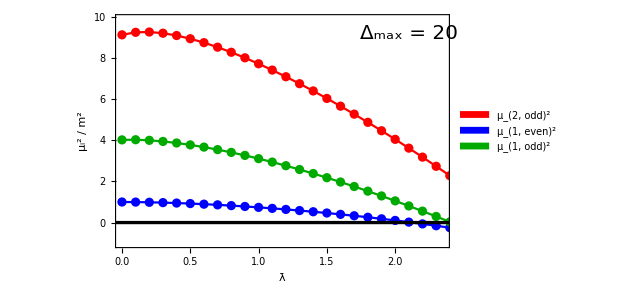

```mathematica
zero=Plot[0,{x,-0.1Max[λlist],1.1Max[λlist]},PlotStyle->{Black,Thickness[0.005]}];
data=Flatten[{dataOdd,dataEven},1];
exper=ListPlot[data,Frame->True,FrameStyle->Thickness[0.002],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["λ̄",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475,PlotRange->{{0,2.35},{-1,9.9}},Epilog->{Inset[Style["Δ_max = "<>ToString[Dmax],FontFamily->"Times",FontSize->20],{2.1,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2","μ_(1, even)^2","μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]];
fit=ListLinePlot[data,PlotStyle->{{Red},{Blue},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
Show[exper,fit,zero]
```

## Convergence with Δ_max (Figure 14)

## Load Data

```mathematica
(* Load Hamiltonian matrices. These matrices include both odd and even particle-number states. *)
binaryGet[name_]:=Import[name]//BinaryDeserialize;
SetDirectory[NotebookDirectory[]];
fullMassMatrix=binaryGet["ScalarMassD"<>ToString[DMAX]<>".WXF"];                        (* Mass Matrix *)
fullNtoNMatrix=binaryGet["ScalarPhi4NtoND"<>ToString[DMAX]<>".WXF"];               (* ϕ^4(n->n) *)
fullNtoN2Matrix=binaryGet["ScalarPhi4NtoN2D"<>ToString[DMAX]<>".WXF"];          (* ϕ^4(n->n+2) *)
```

## Compute Mass Gap vs Δ_max for Odd-Particle Sector

### Define useful functions

```mathematica
(* 'massFuncOdd' extracts the mass matrix at a desired Δmax for the odd-particle-number sector given 'fullMassMatrix' (with DMAX ≥ Δmax). *) 
massFuncOdd[Dmax_]:=Module[{i,j,Nmax,count,massTemp},
Nmax=Ceiling[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n-1}]//Length,{n,Nmax}];
massTemp=ConstantArray[{},{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[2i-1,2i-1,1;;count[[i]],1;;count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(* 'intFuncOdd' extracts the ϕ^4 interaction matrix at a desired Δmax for the odd-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix' (with DMAX ≥ Δmax) *)
intFuncOdd[Dmax_]:=Module[{i,j,Nmax,count,intTemp},
Nmax=Ceiling[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n-1}]//Length,{n,Nmax}];
intTemp=ConstantArray[{},{Nmax,Nmax}];
intTemp[[1,1]]={{0}};
For[i=1,i≤Nmax,i++,
If[i≠1,intTemp[[i,i]]=fullNtoNMatrix[[2i-1,2i-1,1;;count[[i]],1;;count[[i]]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[2i-1,2i+1,1;;count[[i]],1;;count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[2i+1,2i-1,1;;count[[i+1]],1;;count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];
```

### Compute lowest eigenvalues vs Δ_max

```mathematica
(* For a chosen coupling λ, compute low eigenvalues vs Subscript[Δ, max] and store data as a list in valListOdd *)
```

```mathematica
DmaxList=Table[Δmax,{Δmax,10,20}];    (* List of Δmax we want to study  *)
nPoints=2;                                                      (* Number of low eigenvalues to compute for each value of Δmax *)

(* To efficiently compute the lowest eigenvalues, it is useful if all eigenvalues are positive. To ensure all eigenvalues are positive, we can add a small overall shift to the eigenvalues before diagonalizing the Hamitonian, then remove this shift after diagonalizing. This shift needs to be large enough to overcome any negative eigenvalues, but small enough to not decrease the precision of the resulting eigenvalues (in practice 50 is generally a safe value) *)
shift=50;

m=1;
λ=0.55;                                                              (* Set value of the coupling *) 
valListOdd=Table[{},{i,Length[DmaxList]}];
Monitor[For[iD=1,iD≤Length[DmaxList],iD++,
mass=massFuncOdd[DmaxList[[iD]]];
int=intFuncOdd[DmaxList[[iD]]];
vals=Eigenvalues[SparseArray[N[full[m^2,4π λ,mass,int]+shift*IdentityMatrix[mass//Length]]],-nPoints,Method->"Arnoldi"];
valListOdd[[iD]]=vals-shift;
],{iD}];
```

## Compute Mass Gap vs Δ_max for Even-Particle Sector

### Define useful functions

```mathematica
(* 'massFuncEven' extracts the mass matrix at a desired Δmax for the even-particle-number sector given 'fullMassMatrix' (with DMAX ≥ Δmax). *) 
massFuncEven[Dmax_]:=Module[{i,j,Nmax,count,massTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
massTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[2i,2i,1;;count[[i]],1;;count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(* 'intFuncEven' extracts the ϕ^4 interaction matrix at a desired Δmax for the even-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix' (with DMAX ≥ Δmax). *)
intFuncEven[Dmax_]:=Module[{i,j,Nmax,count,intTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
intTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=fullNtoNMatrix[[2i,2i,1;;count[[i]],1;;count[[i]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[2i,2i+2,1;;count[[i]],1;;count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[2i+2,2i,1;;count[[i+1]],1;;count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];
```

### Compute lowest eigenvalues vs Δ_max

```mathematica
(* For a chosen coupling λ, compute low eigenvalues vs Subscript[Δ, max] and store data as a list in valListEven *)
```

```mathematica
DmaxList=Table[Δmax,{Δmax,10,20}];       (* List of Δmax we want to study  *)
nPoints=1;                                                           (* Number of low eigenvalues to compute for each value of Δmax *)

(* To efficiently compute the lowest eigenvalues, it is useful if all eigenvalues are positive. To ensure all eigenvalues are positive, we can add a small overall shift to the eigenvalues before diagonalizing the Hamitonian, then remove this shift after diagonalizing. This shift needs to be large enough to overcome any negative eigenvalues, but small enough to not decrease the precision of the resulting eigenvalues (in practice 50 is generally a safe value) *)
shift=50;

m=1;
λ=0.55;                                                                  (* Set value of the coupling *) 
valListEven=Table[{},{i,Length[DmaxList]}];
Monitor[For[iD=1,iD≤Length[DmaxList],iD++,
mass=massFuncEven[DmaxList[[iD]]];
int=intFuncEven[DmaxList[[iD]]];
vals=Eigenvalues[SparseArray[N[full[m^2,4π λ,mass,int]+shift*IdentityMatrix[mass//Length]]],-nPoints,Method->"Arnoldi"];
valListEven[[iD]]=vals-shift;
],{iD}];
```

## Create Figure 13

```mathematica
(* To make plot at a given coupling, set λ as desired when running the Odd- and Even- sector codes above. 
The output of the codes above are 'valListOdd' and 'valListEven', which store the low evals vs Subscript[Δ, max] for the chosen value of λ.
 For plotting, set p below to define horizontal axis in plot to be (Subscript[Δ, max])^-p. For small coupling, p=2 approximately,
   while for near-critical coupling p=1 seems to be a better fit.
   
The example plot below is for λ=0.55 with 10 ≤ Subscript[Δ, max] ≤ 20 and setting p=2. 
*)
```

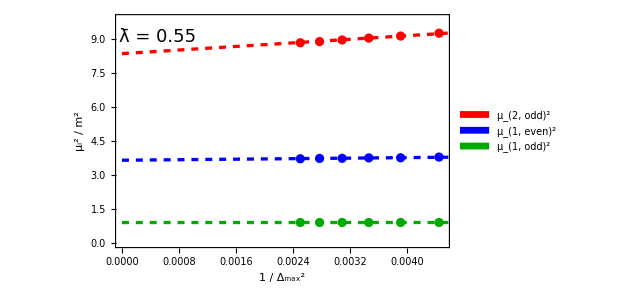

```mathematica
one=valListOdd[[All,2]];                      (* Lowest odd eval vs. Subscript[Δ, max] *) 
two=valListEven[[All,1]];                   (* Lowest even eval vs. Subscript[Δ, max] *) 
three=valListOdd[[All,1]];                 (* 2nd-lowest odd eval vs. Subscript[Δ, max] *) 
p=2;                                                                     (* Define horizontal axis in plot to be (Subscript[Δ, max])^-p *)

data={Thread[{1/DmaxList^p,three}],Thread[{1/DmaxList^p,two}],Thread[{1/DmaxList^p,one}]};
fit1=FindFit[Thread[{1/DmaxList^p,one}],a+b*x,{a,b},x];
fit2=FindFit[Thread[{1/DmaxList^p,two}],a+b*x,{a,b},x];
fit3=FindFit[Thread[{1/DmaxList^p,three}],a+b*x,{a,b},x];
exper=ListPlot[data,Frame->True,FrameStyle->Thickness[0.002],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["1 / Δ_max^2",FontFamily->"Times",FontSize->18,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->18,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475,PlotRange->{{0,0.0045},{0,9.9}},Epilog->{Inset[Style["λ̄ = 0.55",FontFamily->"Times",FontSize->18],{0.0005,9.11}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2","μ_(1, even)^2","μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.65}]];
line=Plot[{(a+b*x)/.fit3,(a+b*x)/.fit2,(a+b*x)/.fit1},{x,0,1.05*Max[1/DmaxList^p]},PlotStyle->{{Red,Dashed,Thickness[0.005]},{Blue,Dashed,Thickness[0.005]},{Darker[Green],Dashed,Thickness[0.005]}}];
Show[exper,line]
```

## Spectral Densities (Figures 15 - 18)

## Compute Overlaps with Basis States

ONLY NEEDS TO BE RUN ONCE FOR A GIVEN DMAX

To compute spectral densities for an operator (such as ϕ^n), we first need the overlaps of our basis states with that operator. This section loads the primary operator basis and computes the overlap of the basis states with ϕ^n up to some maximum value of n (set below). The overlaps are then saved, and can be loaded to compute spectral densities. This procedure only needs to be run once for a given value of DMAX (once the basis has been constructed).

### Load Basis

```mathematica
(* This function converts WXF files into a usable format *)
binaryGet[name_]:=Import[name]//BinaryDeserialize;

(* Load the basis *)
basis=binaryGet["BasisBosonD"<>ToString[DMAX]<>".WXF"];
```

### Compute Overlaps of Basis with ϕ^n

```mathematica
(* Set maximum particle number to compute overlap with ϕ^n *)
nMax=6;

(* Define function computing overlap of ϕ^n with single monomial *)
overlapMono[k_,n_]:=(n!)/Gamma[Total[k]] √((Gamma[2Total[k]]Length[Permutations[k]])/((4π)^(n-1)Length[k]!(Times@@k)))//N;

(* Create a placeholder for the list of basis state overlaps *)
overlaps=ConstantArray[{},nMax];

(* There is only one single-particle state (∂ϕ), with a trivial overlap with ϕ *)
overlaps[[1]]={1};

(* Proceed by particle number up to nMax *)
Monitor[For[nPart=2,nPart≤nMax,nPart++,
temp={};
(* For each particle number, proceed by scaling dimension up to DMAX *)
For[Δ=nPart,Δ≤DMAX,Δ++,
(* Construct the list of monomials at this particle number and degree *)
klist=IntegerPartitions[Δ,{nPart}];
(* Extract the coefficients of the primary basis states in terms of monomials *)
coeffs=basis[[1,Δ-nPart+1,nPart]];
If[Length[coeffs]>0,
(* First compute a table of overlaps of monomials with ϕ^n *)
overlapArray=Table[overlapMono[k,nPart],{k,klist}];
(* Use this array to obtain the overlap of basis states with ϕ^n *)
temp=Join[temp,coeffs.overlapArray];
];
];
overlaps[[nPart]]=temp;
],{nPart,Δ}];

(* Save the resulting overlaps *)
DeleteFile["OverlapsD"<>ToString[DMAX]];
Save["OverlapsD"<>ToString[DMAX],{overlaps}];
```

DeleteFile::fdnfnd: Directory or file OverlapsD20 not found.

## Diagonalize Hamiltonian and Compute Spectral Densities

RUN THIS SECTION BEFORE CREATING FIGURES

### Load Data

```mathematica
(* This function converts WXF files into a usable format *)
binaryGet[name_]:=Import[name]//BinaryDeserialize;

(* Load mass term and ϕ^4 interaction matrices *)
fullMassMatrix=binaryGet["ScalarMassD"<>ToString[DMAX]<>".WXF"];
fullNtoNMatrix=binaryGet["ScalarPhi4NtoND"<>ToString[DMAX]<>".WXF"];
fullNtoN2Matrix=binaryGet["ScalarPhi4NtoN2D"<>ToString[DMAX]<>".WXF"];

(* Load overlaps of basis states with ϕ^n *)
overlaps=Get["OverlapsD"<>ToString[DMAX]];
```

### Define Useful Functions

```mathematica
(* 'massFuncEven' extracts the mass matrix at a desired Δmax for the even-particle-number sector given 'fullMassMatrix' (with DMAX ≥ Δmax). *) 
massFuncEven[Dmax_]:=Module[{i,j,Nmax,count,massTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
massTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[2i,2i,1;;count[[i]],1;;count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(* 'intFuncEven' extracts the ϕ^4 interaction matrix at a desired Δmax for the even-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix' (with DMAX ≥ Δmax). *)
intFuncEven[Dmax_]:=Module[{i,j,Nmax,count,intTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
intTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=fullNtoNMatrix[[2i,2i,1;;count[[i]],1;;count[[i]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[2i,2i+2,1;;count[[i]],1;;count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[2i+2,2i,1;;count[[i+1]],1;;count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];

(* Modified version of Eigensystem which sorts the eigenvalues by actual value (rather than absolute value) *)
eigensys[mat_]:=Eigensystem[mat]//Transpose//Sort//Transpose;

(* Location of the first and last basis state of a given particle number in the full list of basis states at Dmax *)
first[n_,Dmax_]:=Sum[IntegerPartitions[Dmax,{nPart}]//Length,{nPart,2,n-2,2}]+1;
last[n_,Dmax_]:=Sum[IntegerPartitions[Dmax,{nPart}]//Length,{nPart,2,n,2}];

(* Compute the overlaps of ϕ^n with a list of vectors (vecs_) written in the primary operator basis, to obtain the integrated spectral density *)
ϕspec[n_,Dmax_,vecs_]:=Table[overlaps[[n,1;;last[n,Dmax]-first[n,Dmax]+1]].vecs[[i,first[n,Dmax];;last[n,Dmax]]],{i,Length[vecs]}];
ϕspecSum[n_,Dmax_,vecs_]:=Accumulate[Abs[ϕspec[n,Dmax,vecs]]^2];

(* Compute the overlaps of (∂ϕ)^n with a list of vectors (vecs_) written in the primary operator basis, to obtain the integrated spectral density *)
dϕspec[n_,Dmax_,vecs_]:=Table[vecs[[i,first[n,Dmax]]],{i,Length[vecs]}];
dϕspecSum[n_,Dmax_,vecs_]:=Accumulate[Abs[dϕspec[n,Dmax,vecs]]^2];

(* Compute the overlaps of T_(+-)=(1/2 m^2+1/(16π)λ)ϕ^2+1/(4!)λϕ^4 with a list of vectors (vecs_) written in the primary operator basis, to obtain the integrated spectral density. *)
Tspec[msq_,λ_,Dmax_,vecs_]:=Table[(1/2*msq+1/(16π)*λ)*overlaps[[2,1;;last[2,Dmax]-first[2,Dmax]+1]].vecs[[i,first[2,Dmax];;last[2,Dmax]]]+1/(4!)*λ*overlaps[[4,1;;last[4,Dmax]-first[4,Dmax]+1]].vecs[[i,first[4,Dmax];;last[4,Dmax]]],{i,Length[vecs]}];
TspecSum[msq_,λ_,Dmax_,vecs_]:=Accumulate[Abs[Tspec[msq,λ,Dmax,vecs]]^2];
```

### Set Values for Δmax, Diagonalize Hamiltonian, and Compute Spectral Densities

```mathematica
(*
When comparing spectral densities for different values of Δmax, it is better to keep the mass gap fixed, rather than the coupling. Here we have saved the values of the coupling needed to obtain particular fixed values for the mass gap, which correspond to the mass gap values used in Figures 15-18 in the paper:

	Free Theory:
	DmaxList={10,15,20,30,40};
		λlist={0.,0.,0.,0.,0.};	

		4 Subscript[m, gap]^2 = 2.:
	 DmaxList={10,15,20,30,40};
		λlist={1.9979324518636514,1.7255365140659333,1.587236881099267,1.4856023878650007,1.44};

		4 Subscript[m, gap]^2 = 1.:
	 DmaxList={10,15,20,30,40};
		λlist={2.582686169283515,2.215496993489899,2.0227396407703115,1.8654195580990531,1.79};

		4 Subscript[m, gap]^2 = 0.5:
	 DmaxList={10,15,20,30,40};
		λlist={2.8616321401630356,2.441417823259675,2.2218024475884315,2.0336260292643225,1.94};

		4 Subscript[m, gap]^2 = 0.25:
	 DmaxList={10,15,20,30,40};
		λlist={2.998643307809559,2.550554745302773,2.3177443564349653,2.1135583559781823,2.01};

		4 Subscript[m, gap]^2 = 0.1:
	 DmaxList={10,15,20,30,40};
		λlist={3.080161589391844,2.6149329065343694,2.374273713280887,2.1603208058325305,2.052};

		4 Subscript[m, gap]^2 = 0.05:
	 DmaxList={10,15,20,30,40};
		λlist={3.107226593793892,2.6362173147841705,2.3929515771888044,2.175718236937771,2.066};

We have provided a section below entitled "Extract Coupling as a Function of Mass Gap (at Fixed Δmax)", which allows the user to compute the coupling needed to obtain any particular value of the mass gap at various Δmax.
*)
```

```mathematica
(* Set the values of Δmax (≤DMAX) to consider, and the corresponding value for the coupling *)
DmaxList={10,15,20};
λlist={2.998643307809559,2.550554745302773,2.3177443564349653};

(* Set the maximum number of low-energy eigenvalues to include in the spectral density *)
nPointsMax=1000;

(* Create placeholders for the eigenvalues, C-function, and spectral density for T_(+-) *)
valList=ConstantArray[{},Length[DmaxList]];
specϕ2List=ConstantArray[{},Length[DmaxList]];
specϕ4List=ConstantArray[{},Length[DmaxList]];
specϕ6List=ConstantArray[{},Length[DmaxList]];
specCList=ConstantArray[{},Length[DmaxList]];
specTList=ConstantArray[{},Length[DmaxList]];

(* Proceed through each value of Δmax, diagonalizing the Hamiltonian and computing the spectral densities *)
For[iD=1,iD≤Length[DmaxList],iD++,
Dmax=DmaxList[[iD]];
λ=λlist[[iD]];
Print["Δmax = "<>ToString[Dmax]];

mass=massFuncEven[Dmax];
int=intFuncEven[Dmax];

nPoints=Min[nPointsMax,Length[mass]];
m=1;

t1=AbsoluteTime[];
Print["Diagonalizing Matrix..."];
{vals,vecs}=eigensys[full[m^2,4π λ,mass,int]];
Print["Diagonalized!"];
valList[[iD]]=vals[[1;;nPoints]];
specϕ2List[[iD]]=ϕspecSum[2,Dmax,vecs][[1;;nPoints]];
specϕ4List[[iD]]=ϕspecSum[4,Dmax,vecs][[1;;nPoints]];
specϕ6List[[iD]]=ϕspecSum[6,Dmax,vecs][[1;;nPoints]];
specCList[[iD]]=dϕspecSum[2,Dmax,vecs][[1;;nPoints]];
specTList[[iD]]=TspecSum[m^2,4π λ,Dmax,vecs][[1;;nPoints]];
t2=AbsoluteTime[];
Print["Time Elapsed: "<>ToString[(t2-t1)/60]];
];
```

Δmax = 10

Diagonalizing Matrix...

Diagonalized!

Time Elapsed: 0.00007112

Δmax = 15

Diagonalizing Matrix...

Diagonalized!

Time Elapsed: 0.00040400

Δmax = 20

Diagonalizing Matrix...

Diagonalized!

Time Elapsed: 0.00223895

## Spectral Densities of ϕ^2 and C-Function (Figure 15)

Plot the integrated spectral density for ϕ^2 for the list of values of Δmax, at fixed mass gap

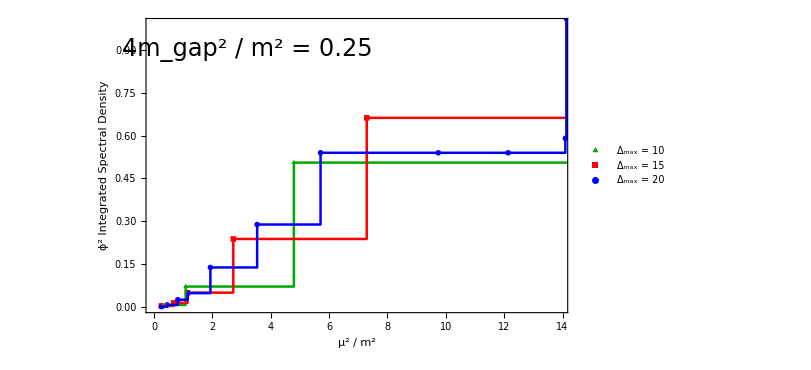

```mathematica
(* If plotting results at λ = 0, we can compare the truncation results to the exact analytical result for free field theory:

thyFig15a=Plot[(2 Log[1/2 (√μsq+√(-4+μsq))])/π,{μsq,4,20},PlotStyle->{Black,Thickness[0.004]}];

*)
gap=Min[valList[[All,1]]];
dataFig15a=ListPlot[Table[Thread[{valList[[iD]],specϕ2List[[iD]]}],{iD,Length[DmaxList]}],Frame->True,FrameStyle->Thickness[0.0015],FrameLabel->{Style["μ^2 / m^2",FontFamily->"Times",FontSize->22,FontColor->Black],Style["ϕ^2 Integrated Spectral Density",FontFamily->"Times",FontSize->22,FontColor->Black],None,None},PlotStyle->{Darker[Green],Red,Blue},PlotMarkers->{{▲,14},{■,14},{●,12}},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{0,13.9},{0,0.99}},PlotLegends->Placed[PointLegend[Table["Δ_max = "<>ToString[DmaxList[[iD]]],{iD,Length[DmaxList]}],LabelStyle->{FontFamily->"Times",20},LegendLayout->{"Row",Length[DmaxList]}],{0.85,0.25}]];
fitFig15a=ListLinePlot[Table[Thread[{valList[[iD]],specϕ2List[[iD]]}],{iD,Length[DmaxList]}],PlotStyle->{{Darker[Green],Thickness[.003]},{Red,Thickness[.003]},{Blue,Thickness[.003]}},InterpolationOrder->0,PlotRange->All];
Show[dataFig15a,fitFig15a,(* thyFig15a, *)Epilog->Inset[Style["4m_gap^2 / m^2 = "<>ToString[gap],FontFamily->"Times",24],{3.2,.9}]]
```

Plot the C-function for the list of values of Δmax, at fixed mass gap

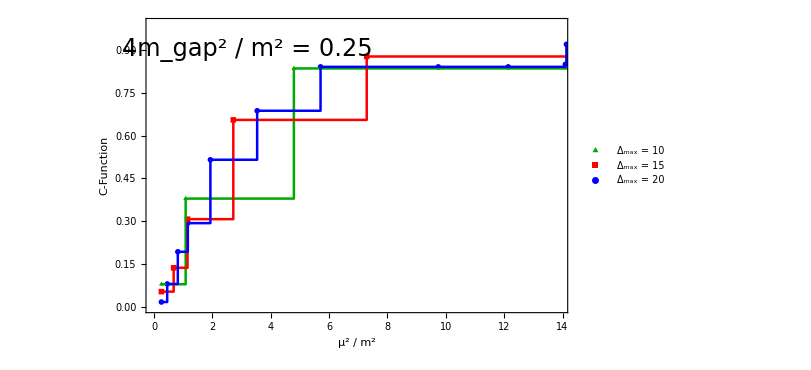

```mathematica
(* If plotting results at λ = 0, we can compare the truncation results to the exact analytical result for free field theory:

thyFig15b=Plot[(2 √((-4+μsq)μsq)+√((-4+μsq)μsq^3))/μsq^2,{μsq,4,20},PlotStyle->{Black,Thickness[0.004]}];

*)
gap=Min[valList[[All,1]]];
dataFig15b=ListPlot[Table[Thread[{valList[[iD]],specCList[[iD]]}],{iD,Length[DmaxList]}],Frame->True,FrameStyle->Thickness[0.0015],FrameLabel->{Style["μ^2 / m^2",FontFamily->"Times",FontSize->22,FontColor->Black],Style["C-Function",FontFamily->"Times",FontSize->22,FontColor->Black],None,None},PlotStyle->{Darker[Green],Red,Blue},PlotMarkers->{{▲,14},{■,14},{●,12}},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{0,13.9},{0,0.99}},PlotLegends->Placed[PointLegend[Table["Δ_max = "<>ToString[DmaxList[[iD]]],{iD,Length[DmaxList]}],LabelStyle->{FontFamily->"Times",20},LegendLayout->{"Row",Length[DmaxList]}],{0.85,0.25}]];
fitFig15b=ListLinePlot[Table[Thread[{valList[[iD]],specCList[[iD]]}],{iD,Length[DmaxList]}],PlotStyle->{{Darker[Green],Thickness[.003]},{Red,Thickness[.003]},{Blue,Thickness[.003]}},InterpolationOrder->0,PlotRange->All];
Show[dataFig15b,fitFig15b,(* thyFig15a, *)Epilog->Inset[Style["4m_gap^2 / m^2 = "<>ToString[gap],FontFamily->"Times",24],{3.2,.9}]]
```

## Universal Behavior of ϕ^n (Figure 16)

Plot the integrated spectral densities for ϕ^2, ϕ^4, and ϕ^6 at fixed Δmax and fixed mass gap, compared with the Ising model integrated spectral density for ϵ

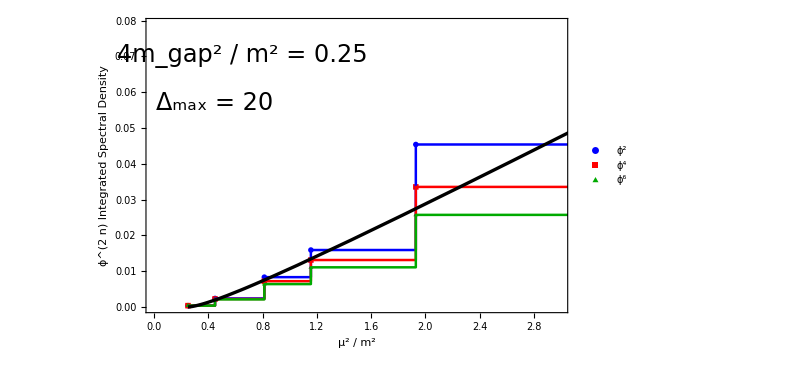

```mathematica
(* Fix overall constant in theory prediction *)
nPoints=5;
gap=valList[[-1,1]];
mgap=Sqrt[Abs[gap/4]];
α=a/.FindFit[Thread[{(valList[[-1,1;;nPoints]]+valList[[-1,2;;nPoints+1]])/2,specϕ2List[[-1,1;;nPoints]]}],{a/(16π)(√(1-gap/x) x+gap/2(Log[gap/2]-Log[-gap/2+(1+√(1-gap/x)) x]))},{a},x];
thyFig16=
Plot[1/(16π)(√(1-gap/x) x+gap/2(Log[gap/2]-Log[-gap/2+(1+√(1-gap/x)) x])),{x,gap,20},PlotStyle->{Black,Thickness[0.004]}];

(* Rescale data by overall coefficient *) 
ratio4=specϕ2List[[-1,1]]/specϕ4List[[-1,1]];
ratio6=specϕ2List[[-1,1]]/specϕ6List[[-1,1]];

(* Plot data *)
dataFig16=ListPlot[{Thread[{valList[[-1]],1/α*specϕ2List[[-1]]}],Thread[{valList[[-1]],1/α*ratio4*specϕ4List[[-1]]}],Thread[{valList[[-1]],1/α*ratio6*specϕ6List[[-1]]}]},Frame->True,FrameStyle->Thickness[0.0015],PlotStyle->{Blue,Red,Darker[Green]},PlotMarkers->{{●,12},{■,14},{▲,14}},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{0,2.99},{0,.079}},PlotLegends->Placed[PointLegend[{"ϕ^2","ϕ^4","ϕ^6"},LabelStyle->{FontFamily->"Times",22},LegendLayout->{"Column",1}],{0.1,0.4}],FrameLabel->{Style["μ^2 / m^2",FontFamily->"Times",FontSize->22,FontColor->Black],Style["ϕ^(2  n) Integrated Spectral Density",FontFamily->"Times",FontSize->20,FontColor->Black],None,None}];
fitFig16=ListLinePlot[{Thread[{valList[[-1]],1/α*specϕ2List[[-1]]}],Thread[{valList[[-1]],1/α*ratio4*specϕ4List[[-1]]}],Thread[{valList[[-1]],1/α*ratio6*specϕ6List[[-1]]}]},PlotStyle->{{Blue,Thickness[0.003]},{Red,Thickness[0.003]},{Darker[Green],Thickness[0.003]}},InterpolationOrder->0,PlotRange->All];
plot1=Show[dataFig16,fitFig16,thyFig16,Epilog->{Inset[Style["Δ_max = "<>ToString[DmaxList[[-1]]],FontFamily->"Times",24],{0.45,.057}],Inset[Style["4m_gap^2 / m^2 = "<>ToString[gap],FontFamily->"Times",24],{.65,.07}]}]
```

## Stress Tensor Trace (Figure 17)

Plot the integrated spectral density of T_(+_) for the list of values of Δmax, at fixed mass gap, compared with the Ising model prediction

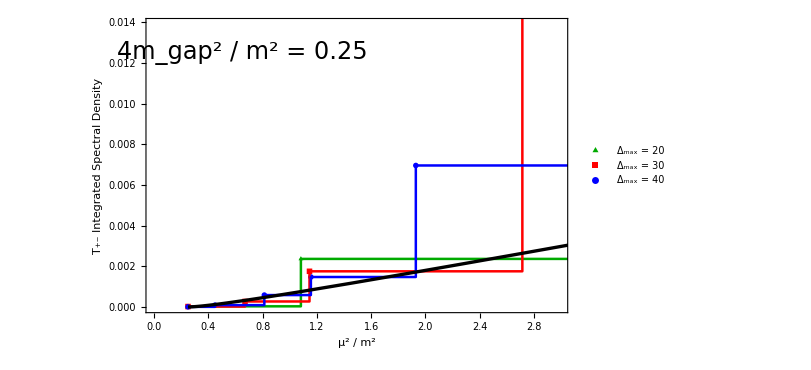

```mathematica
gap=Min[valList[[All,1]]];
dataFig17=ListPlot[Table[Thread[{valList[[iD]],specTList[[iD]]}],{iD,Length[DmaxList]}],Frame->True,FrameStyle->Thickness[0.0015],
FrameLabel->{Style["μ^2 / m^2",FontFamily->"Times",FontSize->22,FontColor->Black],Style["T_(+-) Integrated Spectral Density",FontFamily->"Times",FontSize->22,FontColor->Black],None,None},PlotStyle->{Darker[Green],Red,Blue},PlotMarkers->{{▲,14},{■,14},{●,12}},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{0,2.99},{0,0.0139}},PlotLegends->Placed[PointLegend[{"Δ_max = 20","Δ_max = 30","Δ_max = 40"},LabelStyle->{FontFamily->"Times",22},LegendLayout->{"Row",3}],{0.16,0.5}] ];
fitFig17=ListLinePlot[Table[Thread[{valList[[iD]],specTList[[iD]]}],{iD,Length[DmaxList]}],PlotStyle->{{Darker[Green],Thickness[.003]},{Red,Thickness[.003]},{Blue,Thickness[.003]}},InterpolationOrder->0,PlotRange->All];
thyFig17=Plot[(gap (√(1-gap/μsq) μsq-gap ArcTanh[√(1-gap/μsq)]))/(64 π),{μsq,gap,20},PlotStyle->{Black,Thickness[0.004]}];
Show[dataFig17,fitFig17,thyFig17,Epilog->{Inset[Style["4m_gap^2 / m^2 = "<>ToString[gap],FontFamily->"Times",24],{.65,.0125}]}]
```

## C-Function Near Criticality (Figure 18)

Plot the IR behavior of the C-function for the list of values of Δmax, at fixed mass gap

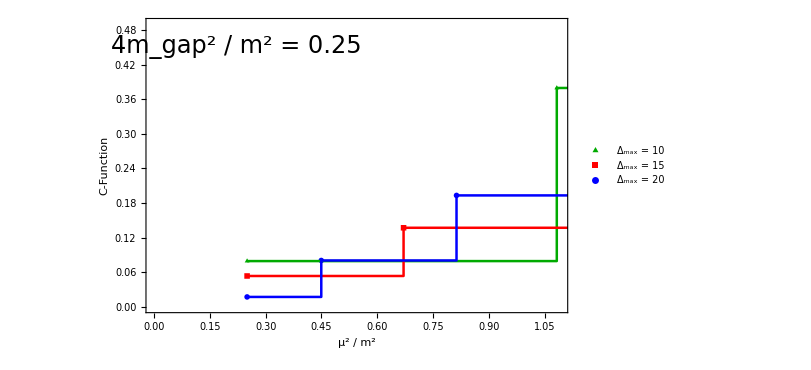

```mathematica
gap=Min[valList[[All,1]]];
dataFig18a=ListPlot[Table[Thread[{valList[[iD]],specCList[[iD]]}],{iD,Length[DmaxList]}],Frame->True,FrameStyle->Thickness[0.0015],FrameLabel->{Style["μ^2 / m^2",FontFamily->"Times",FontSize->22,FontColor->Black],Style["C-Function",FontFamily->"Times",FontSize->22,FontColor->Black],None,None},PlotStyle->{Darker[Green],Red,Blue},PlotMarkers->{{▲,14},{■,14},{●,12}},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{0,1.09},{0,0.49}},PlotLegends->Placed[PointLegend[Table["Δ_max = "<>ToString[DmaxList[[iD]]],{iD,Length[DmaxList]}],LabelStyle->{FontFamily->"Times",22},LegendLayout->{"Row",Length[DmaxList]}],{0.15,0.55}]];
fitFig18a=ListLinePlot[Table[Thread[{valList[[iD]],specCList[[iD]]}],{iD,Length[DmaxList]}],PlotStyle->{{Darker[Green],Thickness[.003]},{Red,Thickness[.003]},{Blue,Thickness[.003]}},InterpolationOrder->0,PlotRange->All];
Show[dataFig18a,fitFig18a,Epilog->{Inset[Style["4m_gap^2 / m^2 = "<>ToString[gap],FontFamily->"Times",FontSize->24,FontColor->Black],{0.22,0.45}]}]
```

Subtract the correction from ∂^2 ϵ from the C-function and compare with the Ising model prediction

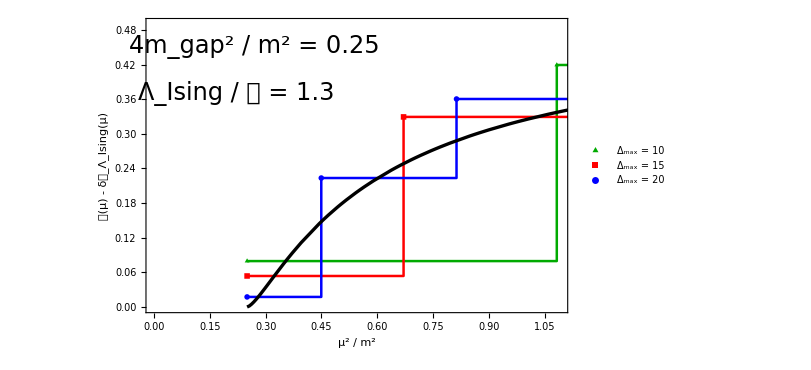

```mathematica
(* Set the parameter Λ *)
Λ=1.3;

(* Theoretical prediction for correction from ∂^2 ϵ, which depends on Subscript[Λ, Ising] *)
gap=Min[valList[[All,1]]];
Ccorr[Λising_,x_]:=(3 √(1-gap/x) x+(3gap)/2 (Log[gap/2]-Log[-gap/2+x+√(1-gap/x) x]))/Λising^2+(3 √gap(2 √(1-gap/x)+Log[gap/2]-Log[-gap/2+x+√(1-gap/x) x]))/Λising;
corrList=Table[Ccorr[Λ,valList[[iD,iV]]],{iD,Length[DmaxList]},{iV,Length[valList[[iD]]]}];

(* Ising model prediction *)
Cising[x_]:=1/2 (1-gap/x)^(3/2);
thyFig18b=Plot[Cising[x],{x,gap,20},PlotStyle->{Black,Thickness[0.004]},PlotRange->All];

(* Subtract ∂^2 ϵ correction from C-function and plot with Ising model prediction *)
dataFig18b=ListPlot[Table[Thread[{valList[[iD]],specCList[[iD]]-corrList[[iD]]}],{iD,Length[DmaxList]}],Frame->True,FrameStyle->Thickness[0.0015],FrameLabel->{Style["μ^2 / m^2",FontFamily->"Times",FontSize->22,FontColor->Black],Style["𝒞(μ) - δ𝒞_Λ_Ising(μ)",FontFamily->"Times",FontSize->22,FontColor->Black],None,None},PlotStyle->{Darker[Green],Red,Blue},PlotMarkers->{{▲,14},{■,14},{●,12}},FrameTicksStyle->14,LabelStyle->Black,ImageSize->600,PlotRange->{{0,1.09},{0,0.49}},PlotLegends->Placed[PointLegend[Table["Δ_max = "<>ToString[DmaxList[[iD]]],{iD,Length[DmaxList]}],LabelStyle->{FontFamily->"Times",22},LegendLayout->{"Row",Length[DmaxList]}],{0.15,0.45}]];
fitFig18b=ListLinePlot[Table[Thread[{valList[[iD]],specCList[[iD]]-corrList[[iD]]}],{iD,Length[DmaxList]}],PlotStyle->{{Darker[Green],Thickness[.003]},{Red,Thickness[.003]},{Blue,Thickness[.003]}},InterpolationOrder->0,PlotRange->All];
Show[dataFig18b,fitFig18b,thyFig18b,Epilog->{Inset[Style["Λ_Ising / 𝓂 = "<>ToString[Λ],FontFamily->"Times",FontSize->24,FontColor->Black],{0.22,0.37}],Inset[Style["4m_gap^2 / m^2 = "<>ToString[gap],FontFamily->"Times",FontSize->24,FontColor->Black],{0.27,0.45}]}]
```

## Extract Coupling as a Function of Mass Gap (at Fixed Δmax)

To compare spectral densities at different values of Δmax, we need to determine the value of the coupling for each Δmax which corresponds to some fixed value of the mass gap. This section scans over values of the coupling, diagonalizing the Hamiltonian at each value, in order to construct an interpolating function that can be used to determine the value of the coupling needed to compute any mass gap.

### Load Data

```mathematica
(* This function converts WXF files into a usable format *)
binaryGet[name_]:=Import[name]//BinaryDeserialize;

(* Load mass term and ϕ^4 interaction matrices *)
fullMassMatrix=binaryGet["ScalarMassD"<>ToString[DMAX]<>".WXF"];
fullNtoNMatrix=binaryGet["ScalarPhi4NtoND"<>ToString[DMAX]<>".WXF"];
fullNtoN2Matrix=binaryGet["ScalarPhi4NtoN2D"<>ToString[DMAX]<>".WXF"];
```

### Define Useful Functions

```mathematica
(* 'massFuncEven' extracts the mass matrix at a desired Δmax for the even-particle-number sector given 'fullMassMatrix' (with DMAX ≥ Δmax). *) 
massFuncEven[Dmax_]:=Module[{i,j,Nmax,count,massTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
massTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[2i,2i,1;;count[[i]],1;;count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(* 'intFuncEven' extracts the ϕ^4 interaction matrix at a desired Δmax for the even-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix' (with DMAX ≥ Δmax). *)
intFuncEven[Dmax_]:=Module[{i,j,Nmax,count,intTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
intTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=fullNtoNMatrix[[2i,2i,1;;count[[i]],1;;count[[i]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[2i,2i+2,1;;count[[i]],1;;count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[2i+2,2i,1;;count[[i+1]],1;;count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];
```

### Set Δmax and Desired Mass Gap and Scan over Couplings

```mathematica
(* Set the value of Δmax *)
Dmax=30;

(* Set the desired mass gap Subscript[μ, gap]^2=4 Subscript[m, gap]^2 (in units of the bare mass) *)
gapGoal=0.05;

(* Scan over values of the coupling, computing the mass gap at each value *)
m=1;
λmax=4;
λmin=0.;
λcount=200;
dλ=(λmax-λmin)/(λcount-1)//N;
λlist=Table[λmin+dλ*(i-1),{i,λcount}];
shift=50;
mass=massFuncEven[Dmax];
int=intFuncEven[Dmax];
gapList=Table[{},{i,Length[λlist]}];
Monitor[For[iL=1,iL≤Length[λlist],iL++,
vals=Eigenvalues[SparseArray[N[full[m^2,4π λlist[[iL]],mass,int]+shift*IdentityMatrix[mass//Length]]],-1,Method->"Arnoldi"];
gapList[[iL]]=vals-shift;
],{iL}];

(* Create an interpolating function based on the data, which can be used to determine the needed value of the coupling for any mass gap *)
coupling=Interpolation[Thread[{gapList,λlist}]];

(* Compute the coupling needed for the desired mass gap *)
coupling[gapGoal]
```

2.17572